The negative combination is non-minimum phase (Sec. 3.6.4)

```mathematica
Clear["Global`*"]
```

```mathematica
Gnmp = (α/(1+0.02s+s^2)+β/(1+0.02s+ s^2/ω^2)) /.α->-1 /.β->2 /.ω->1/2 // Factor // Simplify
```

(0.25+0.005 s-0.5 s^2)/(0.25+0.01 s+1.2501 s^2+0.025 s^3+1. s^4)

Solving for the roots of the numerator shows one positive and one negative zero:

```mathematica
sol=s/.Solve[Numerator[Gnmp]==0,s]
```

{-0.702124,0.712124}

### The positive combination is minimum phase

```mathematica
Gmp= (α/(1+0.02s+s^2)+β/(1+0.02s+ s^2/ω^2))  /.α->1 /.β->2 /.ω->1/2// Factor // Simplify
```

(0.75+0.015 s+1.5 s^2)/(0.25+0.01 s+1.2501 s^2+0.025 s^3+1. s^4)

Here, the zeros are a lightly damped complex - conjugate pair

```mathematica
sol1=s/.Solve[Numerator[Gmp]==0,s]
```

{-0.005-0.707089 ⅈ,-0.005+0.707089 ⅈ}

### Bode Plots for both systems

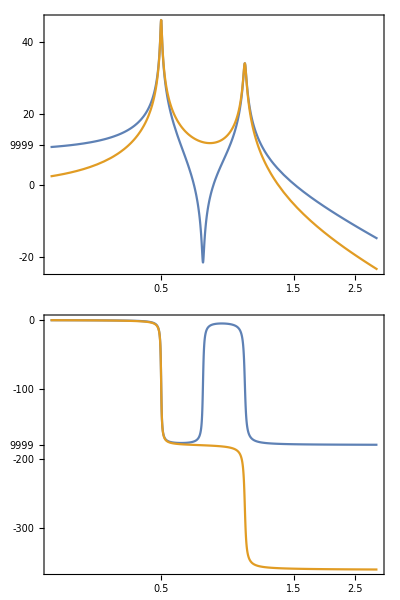

```mathematica
BodePlot[{Gmp,Gnmp},{.2,3}]
```

Now check the mass + 2 - spring system of Doyle et al.

```mathematica
Gdmp =( 1/(k+m s^2)+Subscript[l, u]^2/(k l^2+I0 s^2));
```

minus one to make a prettier phase graph

```mathematica
Gdnmp = 1/(k+m s^2)-Subscript[l, u]^2/(k l^2+I0 s^2);
```

```mathematica
k=1/2; m=2; l=1; I0=1/2; Subscript[l, u]=1/Sqrt[2];
```

```mathematica
(Gdmp- Gmp) // Together // Simplify
```

(s (0.00375+0.000075 s+0.015 s^2+0.00015 s^3+0.0225 s^4))/((1.+s^2) (0.25+1. s^2) (0.25+0.01 s+1.2501 s^2+0.025 s^3+1. s^4))

```mathematica
Gdnmp-Gnmp // Together // Simplify
```

(s (0.00125+0.000025 s-0.005 s^2-0.00005 s^3-0.0175 s^4))/((1.+s^2) (0.25+1. s^2) (0.25+0.01 s+1.2501 s^2+0.025 s^3+1. s^4))

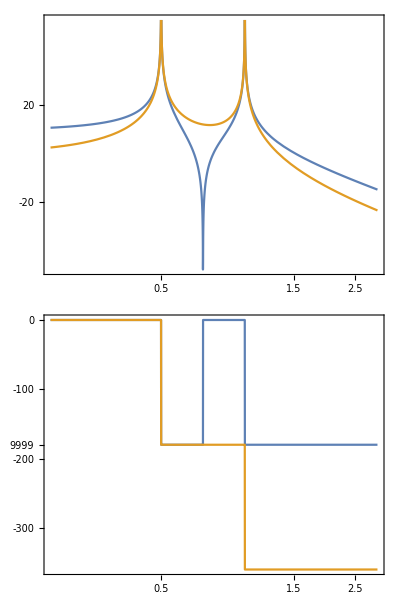

```mathematica
BodePlot[{Gdmp,Gdnmp},{0.2,3}]
```